```mathematica
Me=-4*m*D2^2*D*p^4-16*m*D2^2*D^2*p^3*ct-8*m*D2^2*D^3*p^2+16*m*D2^2*D^4*p*ct+12*m*D2^2*D^5-24*m*D1*D2*D*p^4+16*m*D1*D2*D^2*p^3*ct+32*m*D1*D2*D^3*p^2-16*m*D1*D2*D^4*p*ct-8*m*D1*D2*D^5-4*m*D1^2*D*p^4+8*m*D1^2*D^3*p^2+16*m*D1^2*D^3*p^2*ct^2-32*m*D1^2*D^4*p*ct+12*m*D1^2*D^5+4*m^2*D2^2*p^4+24*m^2*D2^2*D*p^3*ct+32*m^2*D2^2*D^2*p^2-24*m^2*D2^2*D^3*p*ct-36*m^2*D2^2*D^4+24*m^2*D1*D2*p^4-16*m^2*D1*D2*D^2*p^2-16*m^2*D1*D2*D^2*p^2*ct^2+32*m^2*D1*D2*D^3*p*ct-24*m^2*D1*D2*D^4+4*m^2*D1^2*p^4+40*m^2*D1^2*D*p^3*ct-48*m^2*D1^2*D^2*p^2-64*m^2*D1^2*D^2*p^2*ct^2+88*m^2*D1^2*D^3*p*ct-20*m^2*D1^2*D^4-8*m^3*D2^2*p^3*ct-28*m^3*D2^2*D*p^2+36*m^3*D2^2*D^3-16*m^3*D1*D2*p^3*ct-24*m^3*D1*D2*D*p^2+32*m^3*D1*D2*D*p^2*ct^2-64*m^3*D1*D2*D^2*p*ct+72*m^3*D1*D2*D^3-40*m^3*D1^2*p^3*ct+36*m^3*D1^2*D*p^2+80*m^3*D1^2*D*p^2*ct^2-128*m^3*D1^2*D^2*p*ct+52*m^3*D1^2*D^3+4*m^4*D2^2*p^2+8*m^4*D2^2*D*p*ct-12*m^4*D2^2*D^2+8*m^4*D1*D2*p^2-16*m^4*D1*D2*p^2*ct^2+48*m^4*D1*D2*D*p*ct-40*m^4*D1*D2*D^2+4*m^4*D1^2*p^2-32*m^4*D1^2*p^2*ct^2+72*m^4*D1^2*D*p*ct-44*m^4*D1^2*D^2;
```

```mathematica
r=Me p^2(m-d)/.D->d/.D1->1/(d^2-p^2+2((m-d)d-p*(m-d)ct)-m^2)/.D2->1/(m^2-2m d+d^2-p^2)//FullSimplify
```

-((16 (d-m)^2 m p^2 (2 d^2+m^2-2 p^2) (d^2 (d-m)^4-2 ct d (d-m)^4 p-(d-m)^2 (2 d m+ct^2 (d-m) (d+m)) p^2+2 ct (d-m)^2 (d+ct^2 d+m-ct^2 m) p^3+(-ct^2 (d-3 m) (d-m)+m^2) p^4-2 ct d p^5+p^6))/((d-m)^4-2 ct (d-m)^3 p+2 ct (d-m) p^3-p^4)^2)

```mathematica
ri=Assuming[m>d>m/2&&d>p>0,Integrate[r,{ct,-1,1}]]
```

-((2 (d-m) m p (2 d^2+m^2-2 p^2) ((3 d^4-4 d^3 m-5 m^4+2 m^2 p^2+3 p^4-6 d^2 (m^2+p^2)+4 d m (3 m^2+p^2)) Log[(d-m+p)^2]-2 (-2 (d-m) p (d^2-2 d m+5 m^2+p^2)+(3 d^4-4 d^3 m-5 m^4+2 m^2 p^2+3 p^4-6 d^2 (m^2+p^2)+4 d m (3 m^2+p^2)) Log[-d+m+p])))/((d-m+p)^2 (-d+m+p)^2))

```mathematica
ripN[d_]:=NIntegrate[-((2 (d-m) m p (2 d^2+m^2-2 p^2) ((3 d^4-4 d^3 m-5 m^4+2 m^2 p^2+3 p^4-6 d^2 (m^2+p^2)+4 d m (3 m^2+p^2)) Log[(d-m+p)^2]-2 (-2 (d-m) p (d^2-2 d m+5 m^2+p^2)+(3 d^4-4 d^3 m-5 m^4+2 m^2 p^2+3 p^4-6 d^2 (m^2+p^2)+4 d m (3 m^2+p^2)) Log[-d+m+p])))/((d-m+p)^2 (-d+m+p)^2))/.m->1,{p,0,d}]
```

NIntegrate::nlim: p = x is not a valid limit of integration.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0000168772}. NIntegrate obtained -4.55374×10^-23 and 3.01989×10^-26 for the integral and error estimates.

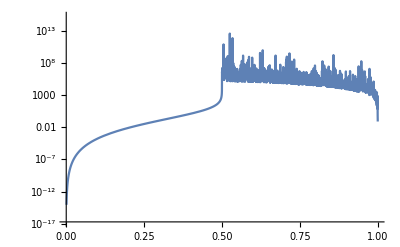

```mathematica
LogPlot[{-ripN[x]},{x,0,1}]
```

```mathematica
sp=Assuming[0<d<1/2,Integrate[ri/.m->1,{p,0,d}]]
```

1/(6 (-1+d) (-1+2 d))(1152 d-7248 d^2+17648 d^3-21520 d^4+13872 d^5-4448 d^6+544 d^7+576 Log[1-2 d]-4200 d Log[1-2 d]+12192 d^2 Log[1-2 d]-18120 d^3 Log[1-2 d]+14832 d^4 Log[1-2 d]-6720 d^5 Log[1-2 d]+1632 d^6 Log[1-2 d]-192 d^7 Log[1-2 d]+240 Log[2] Log[1-2 d]-1470 d Log[2] Log[1-2 d]+4650 d^2 Log[2] Log[1-2 d]-9366 d^3 Log[2] Log[1-2 d]+11976 d^4 Log[2] Log[1-2 d]-9684 d^5 Log[2] Log[1-2 d]+3960 d^6 Log[2] Log[1-2 d]-576 d^7 Log[2] Log[1-2 d]-24 Log[64] Log[1-2 d]+64 d Log[64] Log[1-2 d]-36 d^2 Log[64] Log[1-2 d]-4 d^3 Log[64] Log[1-2 d]+8 d^4 Log[64] Log[1-2 d]+36 d^5 Log[64] Log[1-2 d]+28 d^6 Log[64] Log[1-2 d]-72 d^7 Log[64] Log[1-2 d]+3 d Log[1024] Log[1-2 d]+21 d^2 Log[1024] Log[1-2 d]-81 d^3 Log[1024] Log[1-2 d]+24 d^4 Log[1024] Log[1-2 d]+6 d^5 Log[1024] Log[1-2 d]+108 d^6 Log[1024] Log[1-2 d]-3 d^2 Log[1048576] Log[1-2 d]-18 d^3 Log[1048576] Log[1-2 d]+102 d^4 Log[1048576] Log[1-2 d]-108 d^5 Log[1048576] Log[1-2 d]-48 Log[1-2 d]^2+432 d Log[1-2 d]^2-1392 d^2 Log[1-2 d]^2+2064 d^3 Log[1-2 d]^2-1440 d^4 Log[1-2 d]^2+384 d^5 Log[1-2 d]^2+192 d Log[1-2 d] Log[2-2 d]-1800 d^2 Log[1-2 d] Log[2-2 d]+6432 d^3 Log[1-2 d] Log[2-2 d]-11424 d^4 Log[1-2 d] Log[2-2 d]+10800 d^5 Log[1-2 d] Log[2-2 d]-5208 d^6 Log[1-2 d] Log[2-2 d]+1008 d^7 Log[1-2 d] Log[2-2 d]-30 Log[1-d]+102 d Log[1-d]-138 d^2 Log[1-d]+174 d^3 Log[1-d]-120 d^4 Log[1-d]-60 d^5 Log[1-d]+72 d^6 Log[1-d]-186 Log[2] Log[1-d]+666 d Log[2] Log[1-d]-1950 d^2 Log[2] Log[1-d]+5490 d^3 Log[2] Log[1-d]-9102 d^4 Log[2] Log[1-d]+8712 d^5 Log[2] Log[1-d]-3360 d^6 Log[2] Log[1-d]+432 d^7 Log[2] Log[1-d]+36 Log[64] Log[1-d]-96 d Log[64] Log[1-d]+90 d^2 Log[64] Log[1-d]-90 d^3 Log[64] Log[1-d]+42 d^4 Log[64] Log[1-d]-12 d^5 Log[64] Log[1-d]-150 d^6 Log[64] Log[1-d]+108 d^7 Log[64] Log[1-d]-3 Log[1024] Log[1-d]-21 d Log[1024] Log[1-d]+81 d^2 Log[1024] Log[1-d]-27 d^3 Log[1024] Log[1-d]-27 d^4 Log[1024] Log[1-d]-24 d^5 Log[1024] Log[1-d]-6 d^6 Log[1024] Log[1-d]-108 d^7 Log[1024] Log[1-d]+3 d^2 Log[1048576] Log[1-d]+18 d^3 Log[1048576] Log[1-d]-102 d^4 Log[1048576] Log[1-d]+108 d^5 Log[1048576] Log[1-d]+3 d Log[1099511627776] Log[1-d]+18 d^2 Log[1099511627776] Log[1-d]-99 d^3 Log[1099511627776] Log[1-d]+126 d^4 Log[1099511627776] Log[1-d]-102 d^5 Log[1099511627776] Log[1-d]+108 d^6 Log[1099511627776] Log[1-d]-3 d^2 Log[1152921504606846976] Log[1-d]-18 d^3 Log[1152921504606846976] Log[1-d]+102 d^4 Log[1152921504606846976] Log[1-d]-108 d^5 Log[1152921504606846976] Log[1-d]+96 Log[1-2 d] Log[1-d]-1056 d Log[1-2 d] Log[1-d]+4584 d^2 Log[1-2 d] Log[1-d]-10560 d^3 Log[1-2 d] Log[1-d]+14304 d^4 Log[1-2 d] Log[1-d]-11568 d^5 Log[1-2 d] Log[1-d]+5208 d^6 Log[1-2 d] Log[1-d]-1008 d^7 Log[1-2 d] Log[1-d]-114 Log[1-d]^2+852 d Log[1-d]^2-2604 d^2 Log[1-d]^2+4176 d^3 Log[1-d]^2-3714 d^4 Log[1-d]^2+1740 d^5 Log[1-d]^2-336 d^6 Log[1-d]^2+15 Log[(-1+d)^2]-51 d Log[(-1+d)^2]+69 d^2 Log[(-1+d)^2]-87 d^3 Log[(-1+d)^2]+60 d^4 Log[(-1+d)^2]+30 d^5 Log[(-1+d)^2]-36 d^6 Log[(-1+d)^2]+33 Log[1-d] Log[(-1+d)^2]-210 d Log[1-d] Log[(-1+d)^2]+606 d^2 Log[1-d] Log[(-1+d)^2]-1056 d^3 Log[1-d] Log[(-1+d)^2]+1137 d^4 Log[1-d] Log[(-1+d)^2]-678 d^5 Log[1-d] Log[(-1+d)^2]+168 d^6 Log[1-d] Log[(-1+d)^2]+12 Log[(-1+d)^2]^2-108 d Log[(-1+d)^2]^2+348 d^2 Log[(-1+d)^2]^2-516 d^3 Log[(-1+d)^2]^2+360 d^4 Log[(-1+d)^2]^2-96 d^5 Log[(-1+d)^2]^2-96 (-1+d)^3 (1-6 d+8 d^2) PolyLog[2,1/(2-2 d)]+96 (-1+d)^3 (1-6 d+8 d^2) PolyLog[2,(1-2 d)/(2-2 d)])

```mathematica
p1=SeriesCoefficient[Series[sp,{d,0,6}],5]
```

1/120 (-1536+194082 Log[2]-492 Log[64]+1307 Log[1024]-1360 Log[1048576]-1665 Log[1099511627776]-1840 Log[1152921504606846976])

```mathematica
Series[sp/p1,{d,0,10}]//FullSimplify
```

d^5+(8 d^6)/3+(152 d^7)/21+(118 d^8)/7+(7115 d^9)/189+(5170 d^10)/63+O[d]^11

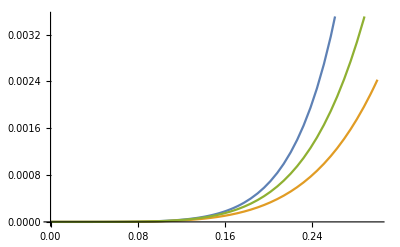

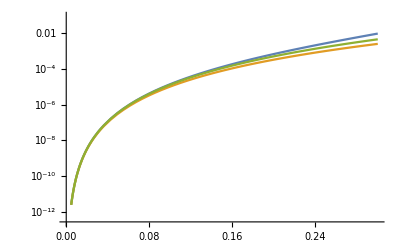

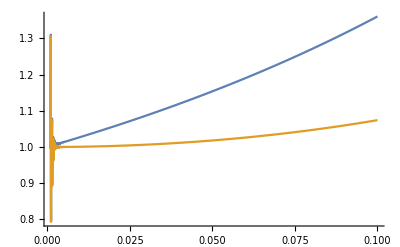

```mathematica
Plot[{sp/p1,d^5,d^5+8/3 d^6},{d,0,0.3}]
LogPlot[{sp/p1,d^5,d^5+8/3 d^6},{d,0,0.3}]
Plot[{sp/p1/d^5,sp/p1/(d^5+8/3 d^6)},{d,10^-3,0.1}]
```

```mathematica
SpD[d_]:=Evaluate[sp]
SpDD[x_]:=SpD[1-x]
```

```mathematica
P1d[x_]:=NIntegrate[(1/y SpDD[x/y]-SpDD[x]) De[y],{y,x,1}]
P2d[x_]:=NIntegrate[SpDD[x] De[y],{y,0,x}]

P1a=Integrate[(1/y SpDD[x/y]-SpDD[x]) De[y],{y,x,1}]
P2a=Integrate[SpDD[x] De[y],{y,0,x}]
```

$Aborted

$Aborted

```mathematica
tab=Table[{x,(P1d[x]+P2d[x])/SpDD[x]},{x,0.7,1-10^-3,0.01}]
```

{{0.7,-2.53789},{0.71,-2.48981},{0.72,-2.44163},{0.73,-2.39293},{0.74,-2.34334},{0.75,-2.29248},{0.76,-2.23995},{0.77,-2.18536},{0.78,-2.12828},{0.79,-2.06827},{0.8,-2.00484},{0.81,-1.93745},{0.82,-1.86548},{0.83,-1.78825},{0.84,-1.70494},{0.85,-1.61463},{0.86,-1.51617},{0.87,-1.40822},{0.88,-1.2891},{0.89,-1.15671},{0.9,-1.00836},{0.91,-0.840522},{0.92,-0.648429},{0.93,-0.425407},{0.94,-0.161695},{0.95,0.157828},{0.96,0.55848},{0.97,1.08771},{0.98,1.85202},{0.99,3.19123}}

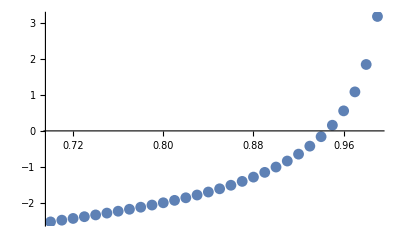

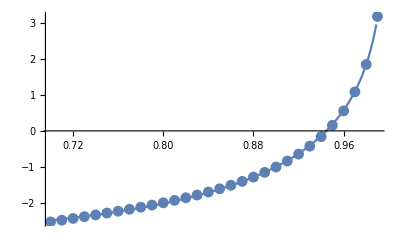

```mathematica
px1=ListPlot[tab]
px2=Plot[-5.75209-3.12388 (-1+x)-1.92755 Log[1-x],{x,0.7,1}];
Show[px1,px2]
```

```mathematica
NonlinearModelFit[tab,{a+b Log[1-x]+c (x-1)},{a,b,c,d},x]
```

FittedModel[-5.75209-3.12388 (-1+x)-1.92755 Log[1-x]]

```mathematica
%163["BestFit"]
```

-5.75209-3.12388 (-1+x)-1.92755 Log[1-x]

```mathematica
%161["BestFitParameters"]
```

{a→-6.1601,b→-2.01966,c→-5.55736,d→-5.20743}

```mathematica
91/15 //N
```

6.06667

```mathematica
139/60//N
```

2.31667